```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.6.0X (April 30, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

## parameters / traits

```mathematica
RuleListSet[{zz->2}]
```

```mathematica
zz
```

2

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞
}]
```

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{δ,i,σ,ρ}
}]
```

```mathematica
δ=1;
```

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{0≤δ≤1,i≥0,σ≥0,ρ≥0}
}]
```

SetModel::badpar: One or more Parameters already defined. Clear them before running SetModel.

$Failed

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
```

{1,i,σ,ρ}

{δ,i,σ,ρ}

```mathematica
δ=.
```

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Trait[x]->{}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{0≤δ≤1,i≥0,σ≥0,ρ≥0}
}]
```

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
```

{δ,i,σ,ρ}

{δ,i,σ,ρ}

```mathematica
δ=1;
```

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
ParameterValues
```

{1,i,σ,ρ}

{δ,i,σ,ρ}

{δ→1,i→i,σ→σ,ρ→ρ}

```mathematica
ClearParameters
```

```mathematica
EcoEvo`Private`parameters
EcoEvo`Private`parnames
ParameterValues
```

{δ,i,σ,ρ}

{δ,i,σ,ρ}

{δ→δ,i→i,σ→σ,ρ→ρ}

```mathematica
SetModel[{
ModelType->"DiscreteTime",
Guild[n]->{
Equation:>(1-δ)Subscript[n, i]+δ Sum[Subscript[n, j],{j,Subscript[𝒩, n]}](i+r[Subscript[x, i],e] Subscript[n, i])/(i Subscript[𝒩, n]+Sum[r[Subscript[x, j],e] Subscript[n, j],{j,Subscript[𝒩, n]}]),
Traits->{-1≤x≤1}},
Aux[e]->{Equation:>de[e]},
Period->∞,
Parameters->{0≤δ≤1,i≥0,σ≥0,ρ≥0}
}]
```

```mathematica
EcoEvo`Private`range[x]
```

Interval[{-1,1}]

## 3) juvenile-adult

```mathematica
Clear[j,a,m,b,dj,da];
SetModel[{
Guild[n]->{Components->{j,a},Traits->{x}},
Transitions:>{
{{Subscript[j, i]⇒Subscript[a, i]},m[Subscript[x[j], i]] Subscript[j, i]},
{{0 Subscript[a, i]⇒Subscript[j, i]},b Subscript[a, i],NormalDistribution[0,σμ]},
{{Subscript[j, i]⇒∅},dj[Subscript[x[j], i]] Subscript[j, i]},
{{Subscript[a, i]⇒∅},da[Subscript[x[a], i]] Subscript[a, i]}
}
}]
```

proc={{{{j_i→-1+j_i,a_i→1+a_i}},m[x[j]_i] j_i},{{{a_i→a_i,j_i→1+j_i}},b a_i,NormalDistribution[0,σμ]},{{{j_i→-1+j_i,∅→1+∅}},dj[x[j]_i] j_i},{{{a_i→-1+a_i,∅→1+∅}},da[x[a]_i] a_i}}

rules={{{j_i→-1+j_i,a_i→1+a_i}},{{a_i→a_i,j_i→1+j_i}},{{j_i→-1+j_i,∅→1+∅}},{{a_i→-1+a_i,∅→1+∅}}}

rates={m[x[j]_i] j_i,b a_i,dj[x[j]_i] j_i,da[x[a]_i] a_i}

eqns={j_i→b a_i-dj[x[j]_i] j_i-m[x[j]_i] j_i,a_i→-da[x[a]_i] a_i+m[x[j]_i] j_i,∅→da[x[a]_i] a_i+dj[x[j]_i] j_i}

percapitaeqns=<|j_i→-dj[x[j]_i]-m[x[j]_i]+(b a_i)/j_i,a_i→-da[x[a]_i]+(m[x[j]_i] j_i)/a_i,∅→(da[x[a]_i] a_i)/∅+(dj[x[j]_i] j_i)/∅|>

ReplaceAll::reps: {Guild[n]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x[j]_i,x[a]_i}

fgs[n]={j_i→{-dj'[x[j]_i]-m'[x[j]_i],0},a_i→{(j_i m'[x[j]_i])/a_i,-da'[x[a]_i]},∅→{(j_i dj'[x[j]_i])/∅,(a_i da'[x[a]_i])/∅}}

ReplaceAll::reps: {Trait[x,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads Trait and List at positions 1 and 2 are expected to be the same.

ColorData::notent: Color/.Join[Trait[x],{Components→{j,a},Traits→{x}},{Color→EEReds}] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

Join::heads: Heads Trait and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]/.EcoEvo`Private`AddTraitts
EvoEqns[{Subscript[𝒩, n]->1}]
```

{j_1'[t]==b a_1[t]-dj[x[j]_1[t]] j_1[t]-m[x[j]_1[t]] j_1[t],a_1'[t]==-da[x[a]_1[t]] a_1[t]+m[x[j]_1[t]] j_1[t]}

{x[j]_1'[t]==(b a_1[t] (x[a]_1[t]-x[j]_1[t]))/j_1[t]-dj'[x[j]_1[t]]-m'[x[j]_1[t]],x[a]_1'[t]==(m[x[j]_1[t]] j_1[t] (-x[a]_1[t]+x[j]_1[t]))/a_1[t]-da'[x[a]_1[t]]}

## 4) two-patch

```mathematica
Clear[b,d0,d1,d2,d12,d21]
SetModel[{
Guild[n]->{
Components->{n1,n2},
Traits->{x}
},
Transitions:>{
{{Subscript[n1, i]⇒∅},d1[Subscript[x[n1], i]] Subscript[n1, i]+d0 Sum[Subscript[n1, j],{j,Subscript[𝒩, n]}] Subscript[n1, i]},
{{Subscript[n2, i]⇒∅},d2[Subscript[x[n2], i]] Subscript[n2, i]+d0 Sum[Subscript[n2, j],{j,Subscript[𝒩, n]}] Subscript[n2, i]},
{{0 Subscript[n1, i]⇒Subscript[n1, i]},b Subscript[n1, i],NormalDistribution[0,σμ]},
{{0 Subscript[n2, i]⇒Subscript[n2, i]},b Subscript[n2, i],NormalDistribution[0,σμ]},
{{Subscript[n1, i]⇒Subscript[n2, i]},d12 Subscript[n1, i]},
{{Subscript[n2, i]⇒Subscript[n1, i]},d21 Subscript[n2, i]}
}
}];
```

proc={{{{n1_i→-1+n1_i,∅→1+∅}},d1[x[n1]_i] n1_i+d0 n1_i ∑_j^𝒩[n] n1_j},{{{n2_i→-1+n2_i,∅→1+∅}},d2[x[n2]_i] n2_i+d0 n2_i ∑_j^𝒩[n] n2_j},{{{n1_i→n1_i,n1_i→1+n1_i}},b n1_i,NormalDistribution[0,σμ]},{{{n2_i→n2_i,n2_i→1+n2_i}},b n2_i,NormalDistribution[0,σμ]},{{{n1_i→-1+n1_i,n2_i→1+n2_i}},d12 n1_i},{{{n2_i→-1+n2_i,n1_i→1+n1_i}},d21 n2_i}}

rules={{{n1_i→-1+n1_i,∅→1+∅}},{{n2_i→-1+n2_i,∅→1+∅}},{{n1_i→n1_i,n1_i→1+n1_i}},{{n2_i→n2_i,n2_i→1+n2_i}},{{n1_i→-1+n1_i,n2_i→1+n2_i}},{{n2_i→-1+n2_i,n1_i→1+n1_i}}}

rates={d1[x[n1]_i] n1_i+d0 n1_i ∑_j^𝒩[n] n1_j,d2[x[n2]_i] n2_i+d0 n2_i ∑_j^𝒩[n] n2_j,b n1_i,b n2_i,d12 n1_i,d21 n2_i}

eqns={n1_i→b n1_i-d12 n1_i-d1[x[n1]_i] n1_i+d21 n2_i-d0 n1_i ∑_j^𝒩[n] n1_j,∅→d1[x[n1]_i] n1_i+d2[x[n2]_i] n2_i+d0 n1_i ∑_j^𝒩[n] n1_j+d0 n2_i ∑_j^𝒩[n] n2_j,n2_i→d12 n1_i+b n2_i-d21 n2_i-d2[x[n2]_i] n2_i-d0 n2_i ∑_j^𝒩[n] n2_j}

percapitaeqns=<|n1_i→b-d12+(d21 n2_i)/n1_i-(d1[x[n1]_i] n1_i+d0 n1_i ∑_j^𝒩[n] n1_j)/n1_i,∅→(d1[x[n1]_i] n1_i+d0 n1_i ∑_j^𝒩[n] n1_j)/∅+(d2[x[n2]_i] n2_i+d0 n2_i ∑_j^𝒩[n] n2_j)/∅,n2_i→b-d21+(d12 n1_i)/n2_i-(d2[x[n2]_i] n2_i+d0 n2_i ∑_j^𝒩[n] n2_j)/n2_i|>

ReplaceAll::reps: {Guild[n]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x[n1]_i,x[n2]_i}

fgs[n]={n1_i→{-d1'[x[n1]_i],0},∅→{(n1_i d1'[x[n1]_i])/∅,(n2_i d2'[x[n2]_i])/∅},n2_i→{0,-d2'[x[n2]_i]}}

ReplaceAll::reps: {Trait[x,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads Trait and List at positions 1 and 2 are expected to be the same.

ColorData::notent: Color/.Join[Trait[x],{Components→{n1,n2},Traits→{x}},{Color→EEReds}] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

Join::heads: Heads Trait and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]/.EcoEvo`Private`AddTraitts
EvoEqns[{Subscript[𝒩, n]->1}]
```

{n1_1'[t]==b n1_1[t]-d12 n1_1[t]-d1[x[n1]_1[t]] n1_1[t]-d0 n1_1[t]^2+d21 n2_1[t],n2_1'[t]==d12 n1_1[t]+b n2_1[t]-d21 n2_1[t]-d2[x[n2]_1[t]] n2_1[t]-d0 n2_1[t]^2}

{x[n1]_1'[t]==(d21 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]-d1'[x[n1]_1[t]],x[n2]_1'[t]==(d12 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]-d2'[x[n2]_1[t]]}

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]/.EcoEvo`Private`AddTraitts
EvoEqns[{Subscript[𝒩, n]->1}]
```

{n1_1'[t]==0.99 n1_1[t]-0.1 n1_1[t]^2+0.01 n2_1[t]-n1_1[t] (1+x[n1]_1[t])^2,n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]-0.1 n2_1[t]^2-n2_1[t] (-1+x[n2]_1[t])^2}

{x[n1]_1'[t]==-2 (1+x[n1]_1[t])+(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t],x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]-2 (-1+x[n2]_1[t])}

EcoEvoSim: eqns=

{n1_1'[t]==0.99 n1_1[t]-0.1 n1_1[t]^2+0.01 n2_1[t]-n1_1[t] (1+x[n1]_1[t])^2,n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]-0.1 n2_1[t]^2-n2_1[t] (-1+x[n2]_1[t])^2,x[n1]_1'[t]==-2 (1+x[n1]_1[t])+(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t],x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]-2 (-1+x[n2]_1[t])}

EcoEvoSim: ics=

{x[n1]_1[0]==-0.6,x[n2]_1[0]==0.8,n1_1[0]==0.1,n2_1[0]==0.2}

EcoEvoSim: unks=

{n1_1,n2_1,x[n1]_1,x[n2]_1}

EcoEvoSim: bdwhens=

{}

EcoEvoSim: discretevars=

{}

{}

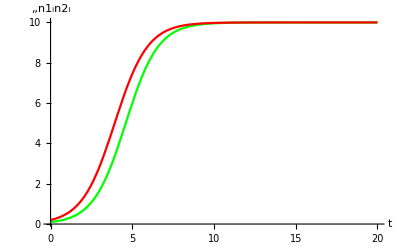

{}

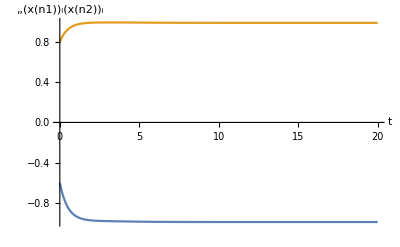

{n1_1→9.99902,n2_1→9.99902,x[n1]_1→-0.990099,x[n2]_1→0.990099}

```mathematica
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.6,Subscript[x[n2], 1]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},20,Verbose->True];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

{}

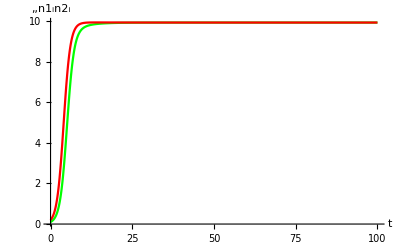

{}

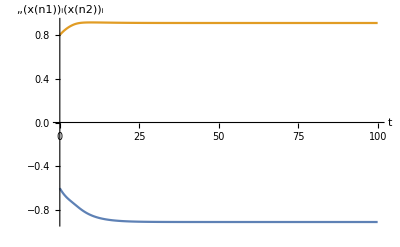

{n1_1→9.91736,n2_1→9.91736,x[n1]_1→-0.909091,x[n2]_1→0.909091}

```mathematica
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.6,Subscript[x[n2], 1]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},{V[x]->0.1},100];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

{}

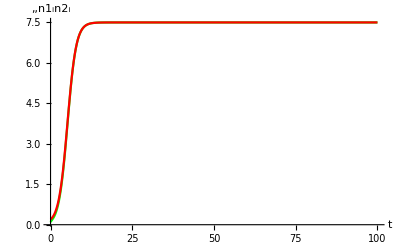

{}

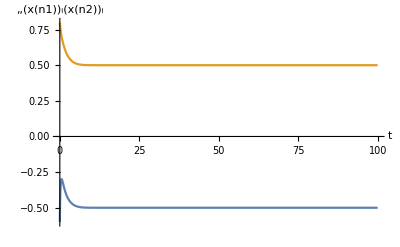

{n1_1→7.5,n2_1→7.5,x[n1]_1→-0.5,x[n2]_1→0.5}

```mathematica
d12=d21=1;
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.6,Subscript[x[n2], 1]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},100];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

{}

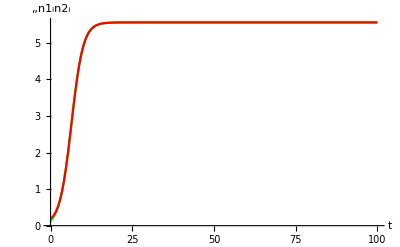

{}

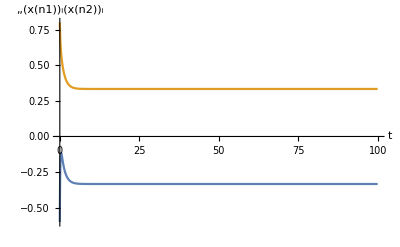

{n1_1→5.55556,n2_1→5.55556,x[n1]_1→-0.333333,x[n2]_1→0.333333}

```mathematica
d12=d21=2;
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.6,Subscript[x[n2], 1]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},100];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

{}

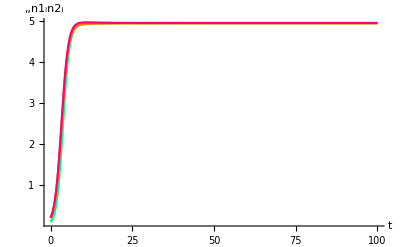

{}

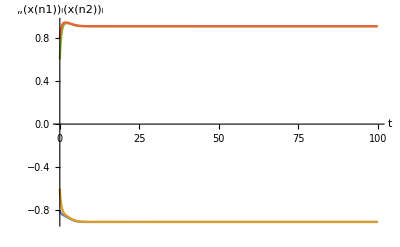

{n1_1→4.95574,n2_1→4.95574,n1_2→4.96161,n2_2→4.96161,x[n1]_1→-0.909091,x[n2]_1→0.909091,x[n1]_2→-0.909091,x[n2]_2→0.909091}

```mathematica
d12=d21=0.1;
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.6,Subscript[x[n1], 2]->-0.6,Subscript[x[n2], 2]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.2},{V[x]->1},100];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

{}

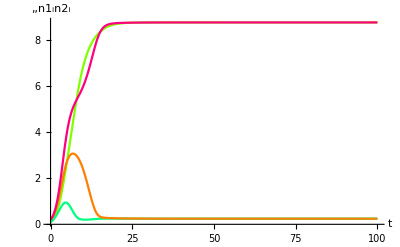

{}

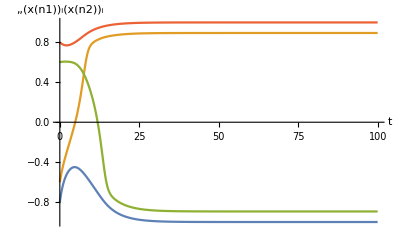

{n1_1→8.78295,n2_1→0.244919,n1_2→0.244919,n2_2→8.78295,x[n1]_1→-0.998528,x[n2]_1→-0.892955,x[n1]_2→0.892955,x[n2]_2→0.998528}

```mathematica
d12=d21=0.1;
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.6,Subscript[x[n1], 2]->-0.6,Subscript[x[n2], 2]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.2},{V[x]->0.1},100];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

{}

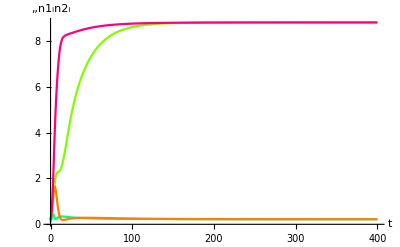

{}

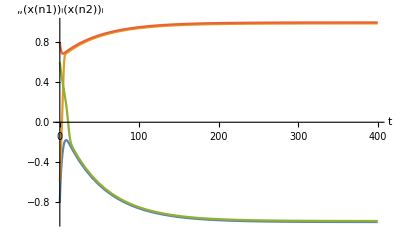

{n1_1→8.80279,n2_1→0.222518,n1_2→0.222466,n2_2→8.80273,x[n1]_1→-0.998388,x[n2]_1→-0.988334,x[n1]_2→0.98856,x[n2]_2→0.998612}

```mathematica
d12=d21=0.1;
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.6,Subscript[x[n1], 2]->-0.6,Subscript[x[n2], 2]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.2},{V[x]->0.01},400];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

```mathematica
FindEcoEvoEq[{Subscript[n1, 1]->8.802785846190918,Subscript[n2, 1]->0.22251781222341158,Subscript[n1, 2]->0.2224656634137576,Subscript[n2, 2]->8.802733474487484,Subscript[x[n1], 1]->-0.998388316637455,Subscript[x[n2], 1]->-0.9883343074958106,Subscript[x[n1], 2]->0.9885603877420636,Subscript[x[n2], 2]->0.9986121033718064}]
```

FindRoot::nlnum: The function value {-0.1136 (0.0000234181-8.80279 (1.+x_1)^2),«6»,-0.00252723 (0.98856[t]-1. 0.998612[t])+2. (-1.+0.998612[t])} is not a list of numbers with dimensions {8} at {n1_1,n2_1,n1_2,n2_2,x[n1]_1,x[n2]_1,x[n1]_2,x[n2]_2} = {8.80279,0.222518,0.222466,8.80273,-0.998388,-0.988334,0.98856,0.998612}.

Join::heads: Heads FindRoot and List at positions 1 and 2 are expected to be the same.

SortRuleList[Join[FindRoot[EcoEvo`Private`eqns$22242,EcoEvo`Private`unksics$22242],{}],{n1_1,n2_1,n1_2,n2_2,x_1,x[n1]_1,x[n2]_1,x_2,x[n1]_2,x[n2]_2}]

```mathematica
TraitsQ[{Subscript[x[n1], 1]->-0.2,Subscript[x[n2], 1]->0.2}]
```

True

```mathematica
LookUp[Subscript[x[n1], 1]]
```

{gtrait,n,x[n1],1}

{}

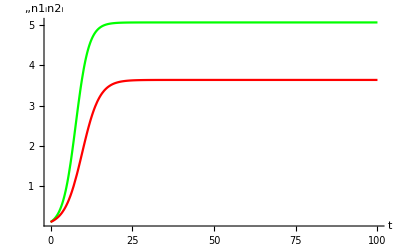

```mathematica
sol=EcoSim[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},100];
PlotDynamics[sol]
```

{}

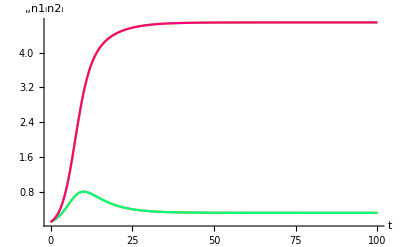

```mathematica
sol=EcoSim[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.1},100];
PlotDynamics[sol]
```

```mathematica
EcoEqns[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3}]
```

{n1_1'[t]==0.5 n1_1[t]-0.1 n1_1[t] (n1_1[t]+n1_2[t])+0.01 n2_1[t],n2_1'[t]==0.01 n1_1[t]+0.35 n2_1[t]-0.1 n2_1[t] (n2_1[t]+n2_2[t]),n1_2'[t]==0.35 n1_2[t]-0.1 n1_2[t] (n1_1[t]+n1_2[t])+0.01 n2_2[t],n2_2'[t]==0.01 n1_2[t]+0.5 n2_2[t]-0.1 n2_2[t] (n2_1[t]+n2_2[t])}

```mathematica
EcoEqns[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3}]
```

{n1_1'[t]==0.5 n1_1[t]-0.1 n1_1[t] (n1_1[t]+n1_2[t])+0.01 n2_1[t],n2_1'[t]==0.01 n1_1[t]-0.7 n2_1[t]-0.1 n2_1[t] (n2_1[t]+n2_2[t]),n1_2'[t]==-0.7 n1_2[t]-0.1 n1_2[t] (n1_1[t]+n1_2[t])+0.01 n2_2[t],n2_2'[t]==0.01 n1_2[t]+0.5 n2_2[t]-0.1 n2_2[t] (n2_1[t]+n2_2[t])}

{}

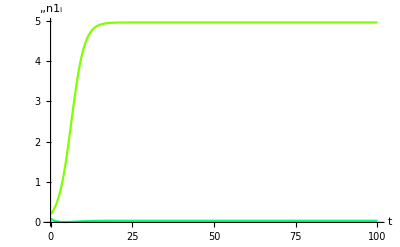

{}

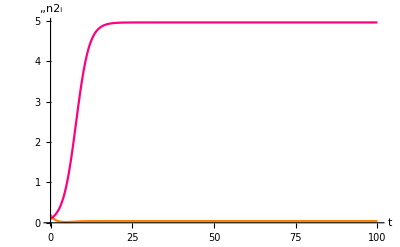

{n1_1→4.95951,n2_1→0.0413264,n1_2→0.0413264,n2_2→4.95951}

```mathematica
sol=EcoSim[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3},{Subscript[n1, 1]->0.2,Subscript[n2, 1]->0.2,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.1},100];
PlotDynamics[sol,n1]
PlotDynamics[sol,n2]
FinalSlice[sol]
```

```mathematica
SolveEcoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→0.1442,n2_1→-7.00206,n1_2→0,n2_2→0},{n1_1→4.85439,n2_1→-7.06867,n1_2→0,n2_2→0},{n1_1→5.00141,n2_1→0.070734,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-7.06867,n2_2→4.85439},{n1_1→0,n2_1→0,n1_2→-7.00206,n2_2→0.1442},{n1_1→0,n2_1→0,n1_2→0.070734,n2_2→5.00141},{n1_1→0.0588264,n2_1→-7.05966,n1_2→-7.05966,n2_2→0.0588264},{n1_1→4.95951,n2_1→0.0413264,n1_2→0.0413264,n2_2→4.95951}}

```mathematica
eq=SolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}}

```mathematica
ExtantSpecies/@eq
```

{{},{n_1},{n_1},{n_1},{n_2},{n_2},{n_2},{n_1,n_2},{n_1,n_2}}

```mathematica
SelectValid[eq]
```

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}}

```mathematica
NSolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3}]
```

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}}

```mathematica
eq=FindEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},{Subscript[n1, 1]->5,Subscript[n2, 1]->0.5,Subscript[n1, 2]->0.5,Subscript[n2, 2]->5}]
```

{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

```mathematica
EcoEigenvalues[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq]
```

{-0.527297,-0.500664,-0.151327,-0.124694}

```mathematica
EcoEvo`Private`eqn[Subscript[n1, 0]]
```

0.99 n1_0+0.01 n2_0-n1_0 (1+x[n1]_0)^2-0.1 n1_0 ∑_j^𝒩[n] n1_j

```mathematica
?Inv
```

```mathematica
?DInv
```

```mathematica
Inv[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,n]
```

```mathematica
Inv[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,n1]
```

```mathematica
DInv[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,Subscript[x[n1], 0]]
```

```mathematica
InvaderQ[n]
```

True

```mathematica
InvaderQ[n1]
```

True

```mathematica
eq
```

{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

```mathematica
LookUp[n]
```

{guild,n}

```mathematica
EcoEvo`Private`Look
```

```mathematica
debug=True;
InvSPS[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,Guild->n]
debug=False;
```

In InvSPS

attributesin={x[n1]_1→-0.3,x[n2]_1→0.2,x[n1]_2→-0.2,x[n2]_2→0.3}

solin={n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

invaderin={}

opts=Guild→n

Set𝒩: (n tnsp=2 insp=None pnsp=2)

InvSPS: sol={n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

invader={}

no invader given

InvSPS: {invtype,invid}={guild ghost,n}

invtraits={}

InvSPS: inveqns={0.99 n1_0-0.1 n1_0 (n1_1+n1_2)+0.01 n2_0-n1_0 (1+x[n1]_0)^2,0.01 n1_0+0.99 n2_0-0.1 n2_0 (n2_1+n2_2)-n2_0 (-1+x[n2]_0)^2}

InvSPS: invunks={n1_0,n2_0}

InvSPS: qsseqns={}

InvSPS: qsssubs={n1_0→0,n2_0→0}

InvSPS: qssunks={}

InvSPS: eigenvalue mode

InvSPS: qsssols={{}}

InvSPS: qsssol={{}}

InvSPS: j={{0.489336-(1+x[n1]_0)^2,0.01},{0.01,0.489336-(-1+x[n2]_0)^2}}

InvSPS: symbolic Jacobian

InvSPS: eigenvalue=0.489336-0.5 Re[(1+x[n1]_0)^2-√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2]

InvSPS: eigenvector={50. (-(1+x[n1]_0)^2+√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2),1}

{0.489336-0.5 ((1+x[n1]_0)^2-√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2),{n1_0→50. (-(1+x[n1]_0)^2+√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2),n2_0→1}}

```mathematica
debug=True;
InvSPS[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,n]
debug=False;
```

In InvSPS

attributesin={x[n1]_1→-0.3,x[n2]_1→0.2,x[n1]_2→-0.2,x[n2]_2→0.3}

solin={n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

invaderin=n

opts=

Set𝒩: (n tnsp=2 insp=None pnsp=2)

InvSPS: sol={n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

invader={n}

whole-guild ghost invader

InvSPS: {invtype,invid}={guild ghost,n}

invtraits={}

InvSPS: inveqns={0.99 n1_0-0.1 n1_0 (n1_1+n1_2)+0.01 n2_0-n1_0 (1+x[n1]_0)^2,0.01 n1_0+0.99 n2_0-0.1 n2_0 (n2_1+n2_2)-n2_0 (-1+x[n2]_0)^2}

InvSPS: invunks={n1_0,n2_0}

InvSPS: qsseqns={}

InvSPS: qsssubs={n1_0→0,n2_0→0}

InvSPS: qssunks={}

InvSPS: eigenvalue mode

InvSPS: qsssols={{}}

InvSPS: qsssol={{}}

InvSPS: j={{0.489336-(1+x[n1]_0)^2,0.01},{0.01,0.489336-(-1+x[n2]_0)^2}}

InvSPS: symbolic Jacobian

InvSPS: eigenvalue=0.489336-0.5 Re[(1+x[n1]_0)^2-√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2]

InvSPS: eigenvector={50. (-(1+x[n1]_0)^2+√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2),1}

{0.489336-0.5 ((1+x[n1]_0)^2-√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2),{n1_0→50. (-(1+x[n1]_0)^2+√(0.0004+(-0.489336+(1+x[n1]_0)^2)^2-2 (0.489336-(1+x[n1]_0)^2) (0.489336-(-1+x[n2]_0)^2)+(-0.489336+(-1+x[n2]_0)^2)^2)+(-1+x[n2]_0)^2),n2_0→1}}

```mathematica
debug=True;inv=Inv[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,n1]
debug=False;
```

In InvSPS

attributesin={x[n1]_1→-0.3,x[n2]_1→0.2,x[n1]_2→-0.2,x[n2]_2→0.3}

solin={n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

invaderin=n1

opts=FromInv→True

Set𝒩: (n tnsp=2 insp=None pnsp=2)

InvSPS: sol={n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

invader={n1}

whole-gcomp ghost invader

-0.510664+(0.01 n2_0)/n1_0-2 x[n1]_0-x[n1]_0^2

```mathematica
D[inv,Subscript[x[n1], 0]]
```

-2-2 x[n1]_0

```mathematica
inv/.(Subscript[var_Symbol, 0]->Subscript[var, 0] Subscript[x[var], 0])
```

-0.510664-2 x[n1]_0-x[n1]_0^2+(0.01 n2_0 x[n2]_0)/(n1_0 x[n1]_0)

```mathematica
D[inv/.(Subscript[var_Symbol, 0]->Subscript[var, 0] Subscript[x[var], 0]),Subscript[x[n1], 0]]
```

-2-2 x[n1]_0-(0.01 n2_0 x[n2]_0)/(n1_0 x[n1]_0^2)